# Creación de logos

Autómata celular para crear logos

```mathematica
LogoPattern[iterations_:20]:=Module[{methods,ca},
methods := {
<|"TotalisticCode"->RandomInteger[{1,60}],"Dimension"->2,"Neighborhood"->5|>,
<|"OuterTotalisticCode"->RandomInteger[{1,1023}],"Dimension"->2,"Neighborhood"->5|>,
<|"Dimension"->2,"GrowthDecayCases"->{RandomSample[Range[8],2],RandomSample[Range[8],2]}|>
};
ca ={};
While[ca == {},ca = CellularAutomaton[RandomChoice[methods],{{{1}},0},{{{iterations}}}]];
Return[ca];
];
RenderLogo[ca_,colorPalette_]:=Module[{colorTbl},
colorTbl  = Table[
ca[[i,j]]/.{0->Transparent,1->colorPalette[(√(i^2+j^2))/Length[ca]]}
,{i,1,Length[ca]},{j,1,Length[ca]}
];
Return[ArrayPlot[colorTbl,Frame->False]];
];
```

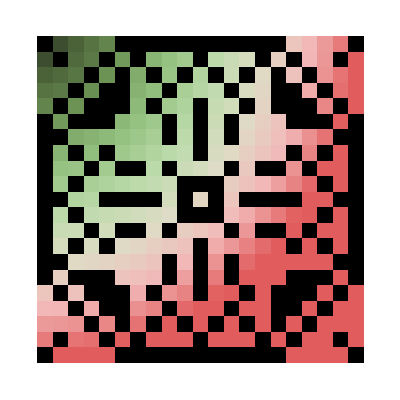

```mathematica
RenderLogo[LogoPattern[20],ColorData["WatermelonColors"]]
```